Project 6 - Curve Fitting
Jacob Schnoor

Problem 1

(1. | 0.629024 | 0.395671 | 0.248886 | 0.156555 | 0.0984769 | 0.0619443 | 0.0389644 | 0.0245095 | 0.0154171 | 0.0096977
1. | 1.47273 | 2.16894 | 3.19428 | 4.70432 | 6.92821 | 10.2034 | 15.0269 | 22.1306 | 32.5925 | 48.0001
1. | 2.12094 | 4.49837 | 9.54076 | 20.2353 | 42.9179 | 91.0261 | 193.06 | 409.469 | 868.458 | 1841.94
1. | 2.65569 | 7.05267 | 18.7297 | 49.7401 | 132.094 | 350.8 | 931.615 | 2474.08 | 6570.37 | 17448.8
1. | 3.19855 | 10.2307 | 32.7234 | 104.667 | 334.784 | 1070.82 | 3425.07 | 10955.3 | 35040.9 | 112080.
1. | 3.78353 | 14.3151 | 54.1617 | 204.922 | 775.33 | 2933.49 | 11098.9 | 41993.2 | 158882. | 601137.
1. | 4.52557 | 20.4808 | 92.6871 | 419.462 | 1898.3 | 8590.91 | 38878.7 | 175948. | 796267. | 3.60356×10^6
1. | 5.26685 | 27.7397 | 146.101 | 769.491 | 4052.79 | 21345.4 | 112423. | 592116. | 3.11858×10^6 | 1.64251×10^7
1. | 6.18095 | 38.2041 | 236.137 | 1459.55 | 9021.42 | 55760.9 | 344655. | 2.13029×10^6 | 1.31672×10^7 | 8.1386×10^7
1. | 6.71801 | 45.1317 | 303.195 | 2036.87 | 13683.7 | 91927.5 | 617570. | 4.14885×10^6 | 2.7872×10^7 | 1.87245×10^8
1. | 7.60757 | 57.8751 | 440.288 | 3349.52 | 25481.7 | 193854. | 1.47476×10^6 | 1.12193×10^7 | 8.53515×10^7 | 6.49318×10^8)

{-1615.41,6783.54,-11365.6,10327.3,-5738.11,2061.36,-488.914,76.0601,-7.46273,0.418588,-0.0102247}

-1615.41+6783.54 x-11365.6 x^2+10327.3 x^3-5738.11 x^4+2061.36 x^5-488.914 x^6+76.0601 x^7-7.46273 x^8+0.418588 x^9-0.0102247 x^10

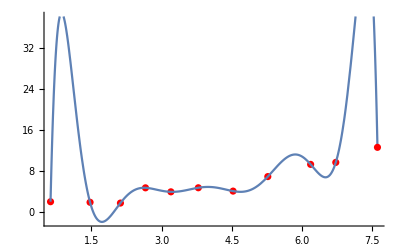

```mathematica
xdata = {0.6290235007022654,1.4727335542075353,2.1209362997671732,2.6556854187053944,3.1985475584469105,3.7835312843658153,4.525568818136562,5.266848558139046,6.1809462326549,6.718014192514695,7.607565703922832};
ydata = {2.0613652424053397,1.9487259038566824,1.7995742786099607,4.758644897025231,3.9818504341982965,4.770544573693086,4.122673558292681,6.942678581702754,9.31185503998008,9.699206285776727,12.62349574764738};
xydata=Transpose[{xdata,ydata}];
vander = Table[xdata[[m]]^(n-1),{m,11},{n,11}];
vander//MatrixForm
vandervars=LinearSolve[vander,ydata]
poly=0;
For[i=1,i≤11,i++,poly+=vandervars[[i]]*x^(i-1)];
poly
pl1=ListPlot[xydata,PlotStyle->Red];
pl2=Plot[poly,{x,xdata[[1]],xdata[[11]]}];
Show[pl1,pl2,PlotRange->All]
```

It would appear to me that the polynomial, p(x), would not be a good approximation for the underlying function the data represents. My intuition tells me that the turbidity of a lake would generally increase as depth increases, give or take a few units. The polynomial represents a drastic fluctuation from peaks to valleys which I do not think is accurate. It goes through all the data points, but I think those exact points are the only spots where it is correct.

Problem 2

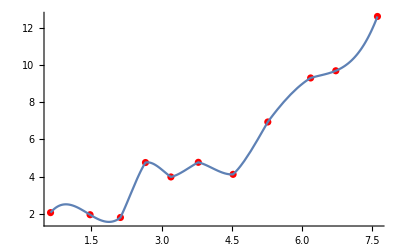

```mathematica
fn=Interpolation[xydata];
pl3=Plot[fn[x],{x,xdata[[1]],xdata[[11]]}];
Show[pl1,pl3,PlotRange->All]
```

The interpolating function is better at not extrapolating to wild extremes like the previous approximation. If for instance the next point has a greater y value, then this line will show continual increasing to get from point a to point b. The other was somewhat unpredictable in that it might increase to 100 first, then come back down to the new value. This approximation is still lacking, however, because it assumes each point represents the exact truth. In a real world scientific setting, every instrument has a degree of uncertainty. To more accurately represent natural phenomena, it is often necessary to sacrifice precise point tracing in order to get a better idea of the overall trend.

Problem 3

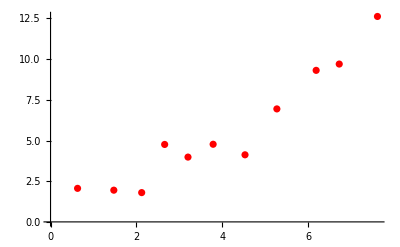

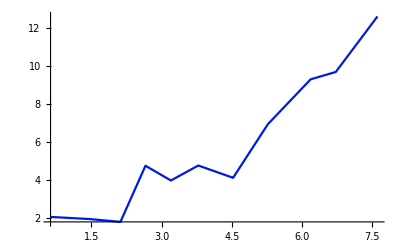
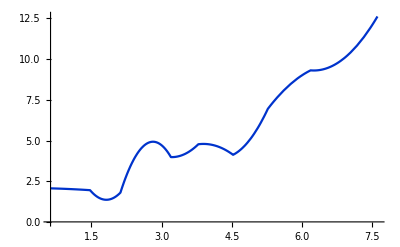
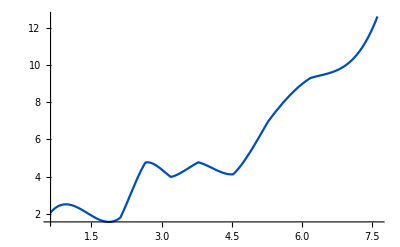
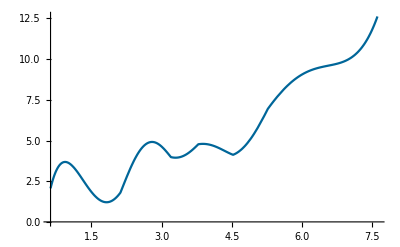
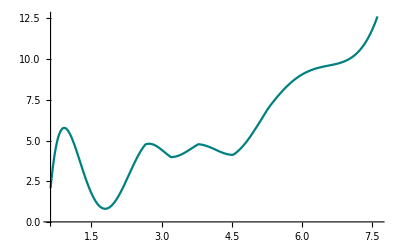
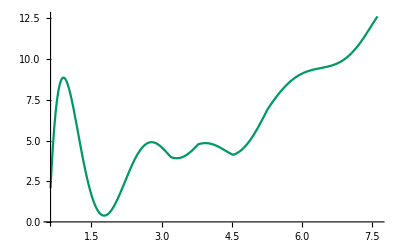
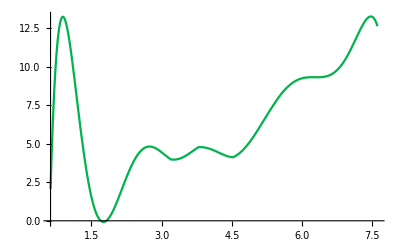

```mathematica
plorder=Table[0,{m,10}];
pl1
For[i=1,i≤10,i++,plorder[[i]]=Plot[Interpolation[xydata,InterpolationOrder->i][x],{x,xdata[[1]],xdata[[11]]},PlotStyle->RGBColor[0,i/10,1-(i/10)]]];
plorder
Show[plorder,pl1]
```

Making the order too high worsens the approximation because it brings back all the problems of using the Vandermonde Matrix method. Any nonzero coefficient for a high order term results in drastic over and underestimation. Basically, in order to perfectly trace along all data points, the function must resemble an extremely eccentric, squiggly line. The function therefore over prioritizes point intersection and loses an accurate picture of the relationship between variables. Personally, I think an order of 3 best represents how turbidity is related to depth in real life. I have no mathematical way of quantifying what signifies “best”. I just think anything lower than 3 looks too jagged while orders greater than 3 look too exaggerated.

Problem 4

(0.629024 | 1
1.47273 | 1
2.12094 | 1
2.65569 | 1
3.19855 | 1
3.78353 | 1
4.52557 | 1
5.26685 | 1
6.18095 | 1
6.71801 | 1
7.60757 | 1)

{1.50345,-0.397356}

-0.397356+1.50345 x

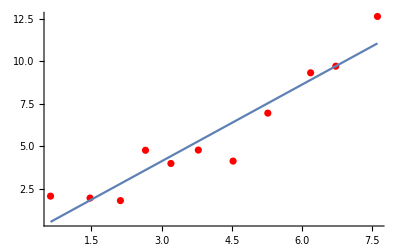

```mathematica
data1=xydata;
For[i=1,i≤11,i++,data1[[i,2]]=1];
data1//MatrixForm
ls=LeastSquares[data1,ydata]
approx=ls[[1]]x+ls[[2]]
pl4=Plot[approx,{x,xdata[[1]],xdata[[11]]}];
Show[pl1,pl4,PlotRange->All]
```

Problem 5

2th Degree Regression
Approximation Equation:	1.9906-0.074185 x+0.190273 x^2

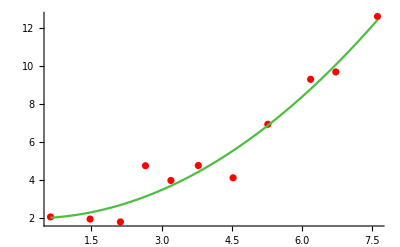

3th Degree Regression
Approximation Equation:	1.43578+0.600915 x-0.00921212 x^2+0.0162993 x^3

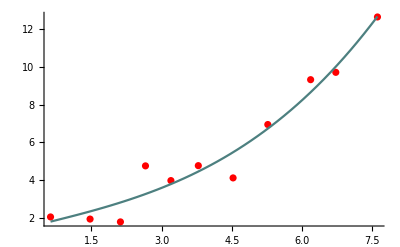

4th Degree Regression
Approximation Equation:	1.52284+0.440818 x+0.071156 x^2+0.00150618 x^3+0.000897842 x^4

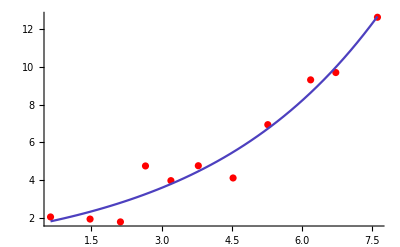

5th Degree Regression
Approximation Equation:	5.15799-8.32556 x+6.44758 x^2-1.93459 x^3+0.259437 x^4-0.0125461 x^5

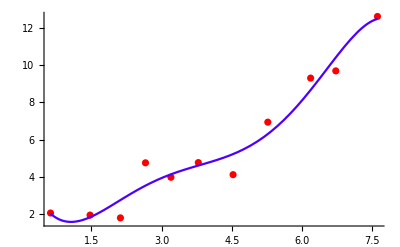

```mathematica
eqns=Table[0,{m,4}];
For[i=3,i≤6,i++,
mat1=Table[xdata[[m]]^(n-1),{m,11},{n,i}];
ls=LeastSquares[mat1,ydata];
For[j=1,j<=i,j++,
eqns[[i-2]]+=ls[[j]]x^(j-1);
];
Print["\n\n",i-1,"th Degree Regression\nApproximation Equation:\t",eqns[[i-2]]];
Print[Show[pl1,Plot[eqns[[i-2]],{x,xdata[[1]],xdata[[11]]},PlotStyle->RGBColor[.3,1-((i-2)/4),(i-2)/4]],PlotRange->All]];
];
```

As far as I can tell, increasing the degree of regression always results in a line that is more responsive to the points without necessarily needing to intersect each one. It is closer to each of the individual points resulting in more waviness. I don’t think it always results in a better fit, however, because most measured phenomena I have seen in scientific fields generally exhibit linear or quadratic correlations. In the event a correlation is quadratic, for instance, approximating it based on a greater degree of regression merely leads to errors becoming magnified.

Problem 6

I think the underlying relationship is quadratic in nature because a linear approximation looks too broad whereas 3rd degree approximations and above involve coefficients that are very near zero. If each additional term is  a_nx^n, then it seems a_n=0 as n→∞. Some guesswork must be done on my end to determine exactly where the cutoff point is based on realistic levels of uncertainty for a measurement apparatus. I think a quadratic approximation (2nd degree) estimates the phenomena the closest, specifically the linear regression method. It best captures the rough trend of all data points without needing to create extreme valleys and troughs.